# Blatt 1

## Teil 1

Setzte die Lichtgeschwindigkeit c

```mathematica
light = c-> 3.*10^8
```

c→3.×10^8

Definiere β als Funktion von der Geschwindigkeit

```mathematica
β[v_]=v/c
```

v/c

Definiere γ als Funktion von β

```mathematica
γ[β_]= 1/(√(1-β^2))
```

1/(√(1-β^2))

Definiere die relativistische Gesamtenergie

```mathematica
w[γ_] = γ*m*c^2
```

c^2 m γ

Definiere die relativistische kinetische Energie

```mathematica
wkin[γ_] = m*c^2*(γ-1)
```

c^2 m (-1+γ)

```mathematica
w[γ[β]]
```

(c^2 m)/(√(1-β^2))

```mathematica
nrel =Series[wkin[γ[β]],{β,0,2}]
```

1/2 c^2 m β^2+O[β]^3

## Teil 2

Allgemeine Formel finden

```mathematica
liste=Solve[ 1/2 c^2 m β^2== n*q*U,β]
```

{{β→-(√2 √n √q √U)/(c √m)},{β→(√2 √n √q √U)/(c √m)}}

Benutzte 2. Ergebnis, da β stets positiv ist.

```mathematica
beta=liste[[2]]
```

{β→(√2 √n √q √U)/(c √m)}

Länge der Driftröhre mit Hilfe von l = v*t und t =T/2 = 1/(2*f)und v = β*c

```mathematica
l=β*c*1/(2*f)
```

(c β)/(2 f)

Länge in Abhängigkeit von n

```mathematica
laenge[n_] =l /. beta /. q-> 1.602*10^-19 /. m-> 1.673*10^-27 /. f-> 100*10^6 /. U-> 100000
```

0.0218811 √n

Erstelle eine Liste n mit der Anzahl der Röhren

```mathematica
n = Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Berechne die Länge jeder einzelnen Röhre in m

```mathematica
laenge[n]
```

{0.0218811,0.0309445,0.0378991,0.0437621,0.0489275,0.0535974,0.0578918,0.061889,0.0656432,0.069194,0.0725713,0.0757982,0.0788933,0.0818714,0.084745,0.0875242,0.0902179,0.0928335,0.0953773,0.0978551,0.100272,0.102631,0.104938,0.107195,0.109405,0.111572,0.113697,0.115784,0.117833,0.119847,0.121829,0.123778,0.125697,0.127587,0.12945,0.131286,0.133097,0.134884,0.136647,0.138388,0.140107,0.141805,0.143484,0.145143,0.146783,0.148405,0.150009,0.151596,0.153167,0.154722,0.156262,0.157787,0.159296,0.160792,0.162274,0.163743,0.165198,0.166641,0.168072,0.16949,0.170897,0.172292,0.173676,0.175048,0.176411,0.177763,0.179104,0.180436,0.181758,0.18307,0.184373,0.185667,0.186952,0.188228,0.189496,0.190755,0.192005,0.193248,0.194483,0.19571,0.19693,0.198141,0.199346,0.200543,0.201733,0.202917,0.204093,0.205263,0.206425,0.207582,0.208732,0.209876,0.211013,0.212145,0.21327,0.21439,0.215503,0.216611,0.217714,0.218811}

Berechne die Gesamtlänge des Linacs in m. Die Röhren sind 2 cm auseinander.

```mathematica
Total[laenge[n]] + 99*20*10^-3
```

16.6723

Plots der Länge der Driftröhren

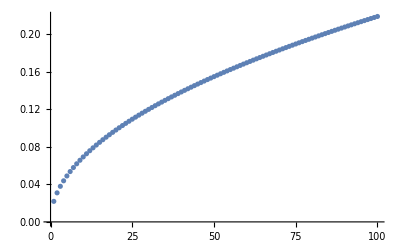

```mathematica
ListPlot[laenge[n]]
```